```mathematica
ClearAll["Global`*"]
SubValues[Derivative]={};
```

```mathematica
(* Problem 4 *)

(* Energies *)
T=(1/2) M y'[t]^2 +(1/2) m (y1'[t]^2+z1'[t]^2) ;
V=m g z1[t];

(* Geometric contrainsts *)
y1[t_] = y[t]+ l Sin[-θ[t]];
z1[t_] = l Cos[-θ[t]];

parameters = {M ->100, m->50, l->2,g->9.81};

T=Collect[T,θ,Simplify]
V=Simplify[V]
L = T-V;
```

1/2 (l^2 m (θ'(t))^2-2 l m θ'(t) cos(θ(t)) y'(t)+(m+M) (y'(t))^2)

g l m cos(θ(t))

```mathematica
(* E-L equations *)
eqn1=Simplify[D[D[L,y'[t]],t]-D[L,y[t]]] - f
eqn2=Simplify[D[D[L,θ'[t]],t]-D[L,θ[t]]]

(* Store nonlinear equations for simulation *)
ytt=Solve[{eqn1==0, eqn2==0}, {y''[t], θ''[t]}][[1,1,2]]
θtt=Solve[{eqn1==0, eqn2==0}, {y''[t], θ''[t]}][[1,2,2]]
```

-f-l m θ''(t) cos(θ(t))+l m (θ'(t))^2 sin(θ(t))+(m+M) y''(t)

l m (-g sin(θ(t))+l θ''(t)-cos(θ(t)) y''(t))

-(f+g m sin(θ(t)) cos(θ(t))-l m (θ'(t))^2 sin(θ(t)))/(m cos^2(θ(t))-m-M)

-(f cos(θ(t))+g m sin(θ(t))+g M sin(θ(t))-l m (θ'(t))^2 sin(θ(t)) cos(θ(t)))/(l (m cos^2(θ(t))-m-M))

```mathematica
eqn1 /. parameters
eqn2 /. parameters
ytt /. parameters
θtt /. parameters
```

-f-100 θ''(t) cos(θ(t))+100 (θ'(t))^2 sin(θ(t))+150 y''(t)

100 (2 θ''(t)-9.81 sin(θ(t))-cos(θ(t)) y''(t))

-(f-100 (θ'(t))^2 sin(θ(t))+490.5 sin(θ(t)) cos(θ(t)))/(50 cos^2(θ(t))-150)

-(f cos(θ(t))-100 (θ'(t))^2 sin(θ(t)) cos(θ(t))+1471.5 sin(θ(t)))/(2 (50 cos^2(θ(t))-150))

```mathematica
(* Linearize the equations *)
leqn1 = eqn1 /. {θ'[t]^2->0, Cos[θ[t]]->1}
leqn2 = eqn2 /. {Sin[θ[t]]->θ[t], Cos[θ[t]]->1}
```

-f-l m θ''(t)+(m+M) y''(t)

l m (-g θ(t)+l θ''(t)-y''(t))

```mathematica
Collect[leqn1,{y[t],θ''[t]}] /. parameters
Collect[leqn2,{y[t],θ''[t]}] /. parameters
```

-f-100 θ''(t)+150 y''(t)

200 θ''(t)+100 (-9.81 θ(t)-y''(t))

```mathematica
(* Let state vector x = (y, θ, yt, θt)*)
```

```mathematica
(* Solve for state space equations *)
sol = Solve[{leqn1==0,leqn2==0},{y''[t],θ''[t]}];
p1 = Collect[sol[[1,1]],{y[t], θ[t]}]
p2 = Collect[sol[[1,2]],{y[t], θ[t]}]
a22 = p1[[2,2]]/.θ[t]->1;
a32 = p2[[2,2]]/.θ[t]->1;
b1 = p1[[2,1]] /. f->1;
b2 = p2[[2,1]] /. f->1;
```

y''(t)→f/M+(g m θ(t))/M

θ''(t)→f/(l M)-(θ(t) (-g m-g M))/(l M)

```mathematica
(* State space matrix *)
A= {{0,0,1,0},
 {0,0,0,1},
{0,a22,0,0},
{0,a32,0,0}} /.parameters
B = {{0},{0},{b1},{b2}} /.parameters
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 4.905 | 0 | 0
0 | 7.3575 | 0 | 0)

(0
0
1/100
1/200)

```mathematica
Q = Transpose[{Flatten[B], Flatten[A.B], Flatten[A.A.B], Flatten[A.A.A.B]} ]
```

(0 | 0.01 | 0. | 0.024525
0 | 0.005 | 0. | 0.0367875
1/100 | 0. | 0.024525 | 0.
1/200 | 0. | 0.0367875 | 0.)

```mathematica
(* Matrix Rank of Q = N, so the system is controllable*)
MatrixRank[Q]
```

4

```mathematica
T1 = {0,0,0,1}.Inverse[Q]
T={Flatten[{T1}],Flatten[{T1.A}], Flatten[{T1.A.A}], Flatten[{T1.A.A.A}]}
```

{-20.3874,40.7747,0.,0.}

(-20.3874 | 40.7747 | 0. | 0.
0. | 0. | -20.3874 | 40.7747
0. | 200. | 0. | 0.
0. | 0. | 0. | 200.)

```mathematica
A1 = T.A.Inverse[T]
B1 = T.B
```

(0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.
0. | 0. | 7.3575 | 0.)

(0.
0.
0.
1.)

```mathematica
Clear[gz,bg];
Gz=Array[gz,4];
B1Gz=Array[bg,{4,4}];
Do[bg[i,j]=B1[[i]] gz[j],{i,1,4},{j,1,4}];
B1Gz
```

({0.} | {0.} | {0.} | {0.}
{0.} | {0.} | {0.} | {0.}
{0.} | {0.} | {0.} | {0.}
{1. gz(1)} | {1. gz(2)} | {1. gz(3)} | {1. gz(4)})

```mathematica
B1Gz = {{0,0,0,0},{0,0,0,0},{0,0,0,0},{gz[1],gz[2],gz[3], gz[4]}}
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
gz(1) | gz(2) | gz(3) | gz(4))

```mathematica
A1star=A1-B1Gz
```

(0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.
0.-gz(1) | 0.-gz(2) | 7.3575-gz(3) | 0.-gz(4))

```mathematica
M1star=s IdentityMatrix[4]-A1star;
cpz=Collect[Det[M1star],s,Simplify]
```

gz(4) s^3+(1. gz(3)-7.3575) s^2+1. gz(2) s+1. gz(1)+s^4+0.

```mathematica
cp0=Collect[(s-s1) (s-s2)(s-s3)(s-s4),s,Simplify]
```

s^4+s^3 (-s1-s2-s3-s4)+s^2 (s1 (s2+s3+s4)+s2 (s3+s4)+s3 s4)+s (-s1 (s2 (s3+s4)+s3 s4)-s2 s3 s4)+s1 s2 s3 s4

```mathematica
g1=Coefficient[cpz,s,3]-Coefficient[cp0,s,3]
g2=Coefficient[cpz,s,2]-Coefficient[cp0,s,2]
g3=Coefficient[cpz,s,1]-Coefficient[cp0,s,1]
g4=Coefficient[cpz,s,0]-Coefficient[cp0,s,0]
```

gz(4)+s1+s2+s3+s4

1. gz(3)-s1 (s2+s3+s4)-s2 (s3+s4)-s3 s4-7.3575

1. gz(2)+s1 (s2 (s3+s4)+s3 s4)+s2 s3 s4

1. gz(1)-s1 s2 s3 s4+0.

```mathematica
Clear[gz,s1,s2,s3,s4];
Solve[{g1==0,g2==0, g3==0,g4==0},{gz[1],gz[2],gz[3],gz[4]}];
{gz[1],gz[2],gz[3],gz[4]}={gz[1],gz[2],gz[3],gz[4]}/.%[[1]];
zgains={gz[1],gz[2],gz[3],gz[4]}
```

{1. s1 s2 s3 s4+0.,-s1 (s2 (s3+s4)+s3 s4)-s2 s3 s4,1. s1 (s2+s3+s4)+1. s2 (s3+s4)+1. s3 s4+7.3575,-s1-s2-s3-s4}

```mathematica
(* Check that gains with original eigenvalues are 0, as expected *)
{s1,s2,s3,s4}=Eigenvalues[A];
Chop[zgains]
```

{0,0,0,0}

```mathematica
Clear[s1,s2,s3,s4]
zgains
xgains=(zgains.T)
```

{1. s1 s2 s3 s4+0.,-s1 (s2 (s3+s4)+s3 s4)-s2 s3 s4,1. s1 (s2+s3+s4)+1. s2 (s3+s4)+1. s3 s4+7.3575,-s1-s2-s3-s4}

{0.-20.3874 (1. s1 s2 s3 s4+0.),40.7747 (1. s1 s2 s3 s4+0.)+200. (1. s1 (s2+s3+s4)+1. s2 (s3+s4)+1. s3 s4+7.3575)+0.,0.-20.3874 (-s1 (s2 (s3+s4)+s3 s4)-s2 s3 s4),200. (-s1-s2-s3-s4)+40.7747 (-s1 (s2 (s3+s4)+s3 s4)-s2 s3 s4)+0.}

```mathematica
(* Assume all poles are Butterworth Poles *)
{s1,s2,s3,s4}=N[(Cos[π/2 + Range[1,4]π/ (4+1)] + ⅈ Sin[π/2 + Range[1,4] π /(4+1)])]
```

{-0.587785+0.809017 ⅈ,-0.951057+0.309017 ⅈ,-0.951057-0.309017 ⅈ,-0.587785-0.809017 ⅈ}

```mathematica
Chop[zgains]
Chop[xgains]
```

{1.,3.07768,11.5936,3.07768}

{-20.3874,2359.49,-62.7458,741.028}

```mathematica
(* Choose state vector = {y, θ, yt, θt}*)
```

```mathematica
X = Array[x,4]
x1t = x[3];
x2t = x[4];
x3t=ytt /.parameters;
x4t = θtt/.parameters;
θ=x[2]; y'[t] =x[3]; θ'[t]=x[4];
xt = {x1t,x2t,x3t,x4t}
```

{x(1),x(2),x(3),x(4)}

{x(3),x(4),-(-100 (x(4))^2 sin(x(2)(t))+490.5 sin(x(2)(t)) cos(x(2)(t))+f)/(50 cos^2(x(2)(t))-150),-(f cos(x(2)(t))+1471.5 sin(x(2)(t))-100 (x(4))^2 sin(x(2)(t)) cos(x(2)(t)))/(2 (50 cos^2(x(2)(t))-150))}

```mathematica
xdot = xt /.{x[2]->x2,x[1][t]->x1[t],x[3]->x3[t],x[4]->x4[t]}
```

{x3(t),x4(t),-(f-100 (x4(t))^2 sin(x2(t))+490.5 sin(x2(t)) cos(x2(t)))/(50 cos^2(x2(t))-150),-(f cos(x2(t))-100 (x4(t))^2 sin(x2(t)) cos(x2(t))+1471.5 sin(x2(t)))/(2 (50 cos^2(x2(t))-150))}

```mathematica
(* Generic differential equations, nonlinear *)
ode1=x1'[t]==xdot[[1]]
ode2=x2'[t]==xdot[[2]]
ode3=x3'[t]==xdot[[3]]
ode4=x4'[t]==xdot[[4]]
```

x1'(t)==x3(t)

x2'(t)==x4(t)

x3'(t)==-(f-100 (x4(t))^2 sin(x2(t))+490.5 sin(x2(t)) cos(x2(t)))/(50 cos^2(x2(t))-150)

x4'(t)==-(f cos(x2(t))-100 (x4(t))^2 sin(x2(t)) cos(x2(t))+1471.5 sin(x2(t)))/(2 (50 cos^2(x2(t))-150))

```mathematica
(* Assume simple parameters, set up differential equations *)
nodes = {ode1 /.parameters,ode2 /.parameters, ode3/.parameters,ode4 /.parameters }
```

{x1'(t)==x3(t),x2'(t)==x4(t),x3'(t)==-(f-100 (x4(t))^2 sin(x2(t))+490.5 sin(x2(t)) cos(x2(t)))/(50 cos^2(x2(t))-150),x4'(t)==-(f cos(x2(t))-100 (x4(t))^2 sin(x2(t)) cos(x2(t))+1471.5 sin(x2(t)))/(2 (50 cos^2(x2(t))-150))}

```mathematica
(* Initial conditions *)
ics={x1[0]==y0, x2[0]==θ0, x3[0]==v0, x4[0]==ω0};
```

```mathematica
(* Our "answer" *)
ans={x1[t],x2[t],x3[t],x4[t]};
```

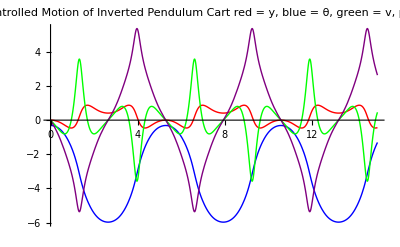

```mathematica
(* Nonliner, uncontrolled simulation *)
f = 0; 
y0=0;θ0=-π/10;v0=0;ω0=0;tf=15;
soln=NDSolve[{nodes,ics},ans,{t,0,tf}];
ny=soln[[1,1,2]];
nθ=soln[[1,2,2]];
nv=soln[[1,3,2]];
nω=soln[[1,4,2]];
Plot[{ny,nθ,nv,nω},{t,0,tf}, PlotStyle->{Red,Blue,Green,Purple},PlotLabel->"Uncontrolled Motion of Inverted Pendulum Cart\n red = y, blue = θ, green = v, purple = ω",
PlotRange->All]
Clear[f,y0,v0,θ0,ω0];
```

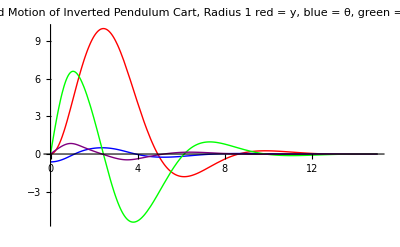

```mathematica
(* Control when θ offset from equalibrium by -π/5 radians *)
(* Butterworth poles, radius 1 *)
{s1,s2,s3,s4} =1N[(Cos[π/2 + Range[1,4]π/ (4+1)] + ⅈ Sin[π/2 + Range[1,4] π /(4+1)])];
f = -Chop[xgains.{x1[t],x2[t],x3[t],x4[t]}];
y0=0;θ0=-π/5;v0=0;ω0=0;tf=15;
soln=NDSolve[{nodes,ics},ans,{t,0,tf}];
ny=soln[[1,1,2]];
nθ=soln[[1,2,2]];
nv=soln[[1,3,2]];
nω=soln[[1,4,2]];
ControlledPicture = Plot[{ny,nθ,nv,nω},{t,0,tf}, PlotStyle->{Red,Blue,Green,Purple},PlotLabel->"Controlled Motion of Inverted Pendulum Cart, Radius 1\nred = y, blue = θ, green = v, Purple = ω",
PlotRange->All]
Clear[f,y0,v0,θ0,ω0];
```

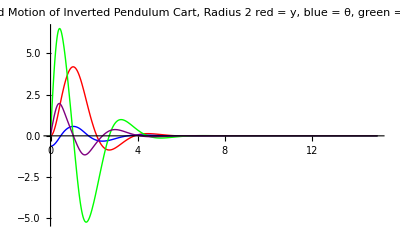

```mathematica
(* Control when θ offset from equalibrium by -π/10 radians *)
(* Butterworth poles, radius 2 *)
{s1,s2,s3,s4}= 2N[(Cos[π/2 + Range[1,4]π/ (4+1)] + ⅈ Sin[π/2 + Range[1,4] π /(4+1)])];
f = -Chop[xgains.{x1[t],x2[t],x3[t],x4[t]}];
y0=0;θ0=-π/5;v0=0;ω0=0;tf=15;
soln=NDSolve[{nodes,ics},ans,{t,0,tf}];
ny=soln[[1,1,2]];
nθ=soln[[1,2,2]];
nv=soln[[1,3,2]];
nω=soln[[1,4,2]];
ControlledPicture = Plot[{ny,nθ,nv,nω},{t,0,tf}, PlotStyle->{Red,Blue,Green,Purple},PlotLabel->"Controlled Motion of Inverted Pendulum Cart, Radius 2\nred = y, blue = θ, green = v, Purple = ω",
PlotRange->All]
Clear[f,y0,v0,θ0,ω0];
```

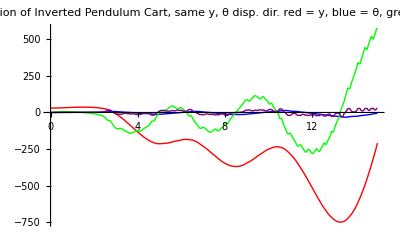

```mathematica
(* High cart displacement to the right, high θ displacement to the right - not controllable *)
{s1,s2,s3,s4} =1N[(Cos[π/2 + Range[1,4]π/ (4+1)] + ⅈ Sin[π/2 + Range[1,4] π /(4+1)])];
f = -Chop[xgains.{x1[t],x2[t],x3[t],x4[t]}];; 
y0=30;θ0=-π/5;v0=0;ω0=0;tf=15;
soln=NDSolve[{nodes,ics},ans,{t,0,tf}];
ny=soln[[1,1,2]];
nθ=soln[[1,2,2]];
nv=soln[[1,3,2]];
nω=soln[[1,4,2]];
ControlledPicture = Plot[{ny,nθ,nv,nω},{t,0,tf}, PlotStyle->{Red,Blue,Green,Purple},PlotLabel->"Controlled Motion of Inverted Pendulum Cart, same y, θ disp. dir. \nred = y, blue = θ, green = v, Purple = ω",
PlotRange->All]
Clear[f,y0,v0,θ0,ω0];
```

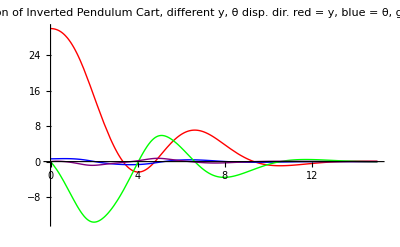

```mathematica
(* High cart displacement to the right, high θ displacement to the left - still controllable *)
{s1,s2,s3,s4} =1N[(Cos[π/2 + Range[1,4]π/ (4+1)] + ⅈ Sin[π/2 + Range[1,4] π /(4+1)])];
f = -Chop[xgains.{x1[t],x2[t],x3[t],x4[t]}];; 
y0=30;θ0=π/5;v0=0;ω0=0;tf=15;
soln=NDSolve[{nodes,ics},ans,{t,0,tf}];
ny=soln[[1,1,2]];
nθ=soln[[1,2,2]];
nv=soln[[1,3,2]];
nω=soln[[1,4,2]];
ControlledPicture = Plot[{ny,nθ,nv,nω},{t,0,tf}, PlotStyle->{Red,Blue,Green,Purple},PlotLabel->"Controlled Motion of Inverted Pendulum Cart, different y, θ disp. dir.\nred = y, blue = θ, green = v, Purple = ω",
PlotRange->All]
Clear[f,y0,v0,θ0,ω0];
```

```mathematica
(* Discussion *)

(* The larger the radius of the Butterworth poles, the smaller the initial θ
  departure must be from the vertical before the simulation breaks down.
 The higher the gains, then, the smaller the value for which θ becomes "too large"
  for the simulation to be accurate. The increase in radius causes the system to 
  reach 0 faster than with the small radius case, but it also increases 
  susceptibility to error arising from using gains derived from the linear 
  case with the nonlinear equations. The initial θ displacement must be 
  smaller for the linear approximation to hold. *)

(* The more the cart and pendulum are initially displaced in the same 
  direction, (right or left) the less likely the system will be controllable.
 If the cart and pendulum are initially displaced in opposite directions, 
   the system is more likely to be controllable. If the θ displacement is too
  large in either direction, of course the system will still be uncontrollable 
  no matter what. *)
```